# Higgs to two photon

### Initialization

```mathematica
Exit[];
```

```mathematica
$Language="English";
SetDirectory[NotebookDirectory[]];
<<FeynArts`
<<FormCalc`
```

FeynArts 3.7

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 4 Jan 12

FormCalc 7.3

by Thomas Hahn

last revised 12 Jan 12

### h → γ γ Matrix Element Calculation

loading generic model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/Lorentz.gen

> $SVMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/Documents/Mathematica/lib/FeynArts-3.7/Models/SM.mod

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 114 counter terms of order 1

> 6 counter terms of order 2

classes model {SM} initialized

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 22 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

Restoring 18 field point(s)

in total: 28 Particles insertions

> Top. 1: 22 diagrams

> Top. 2: 2 diagrams

> Top. 3: 2 diagrams

> Top. 4: 2 diagrams

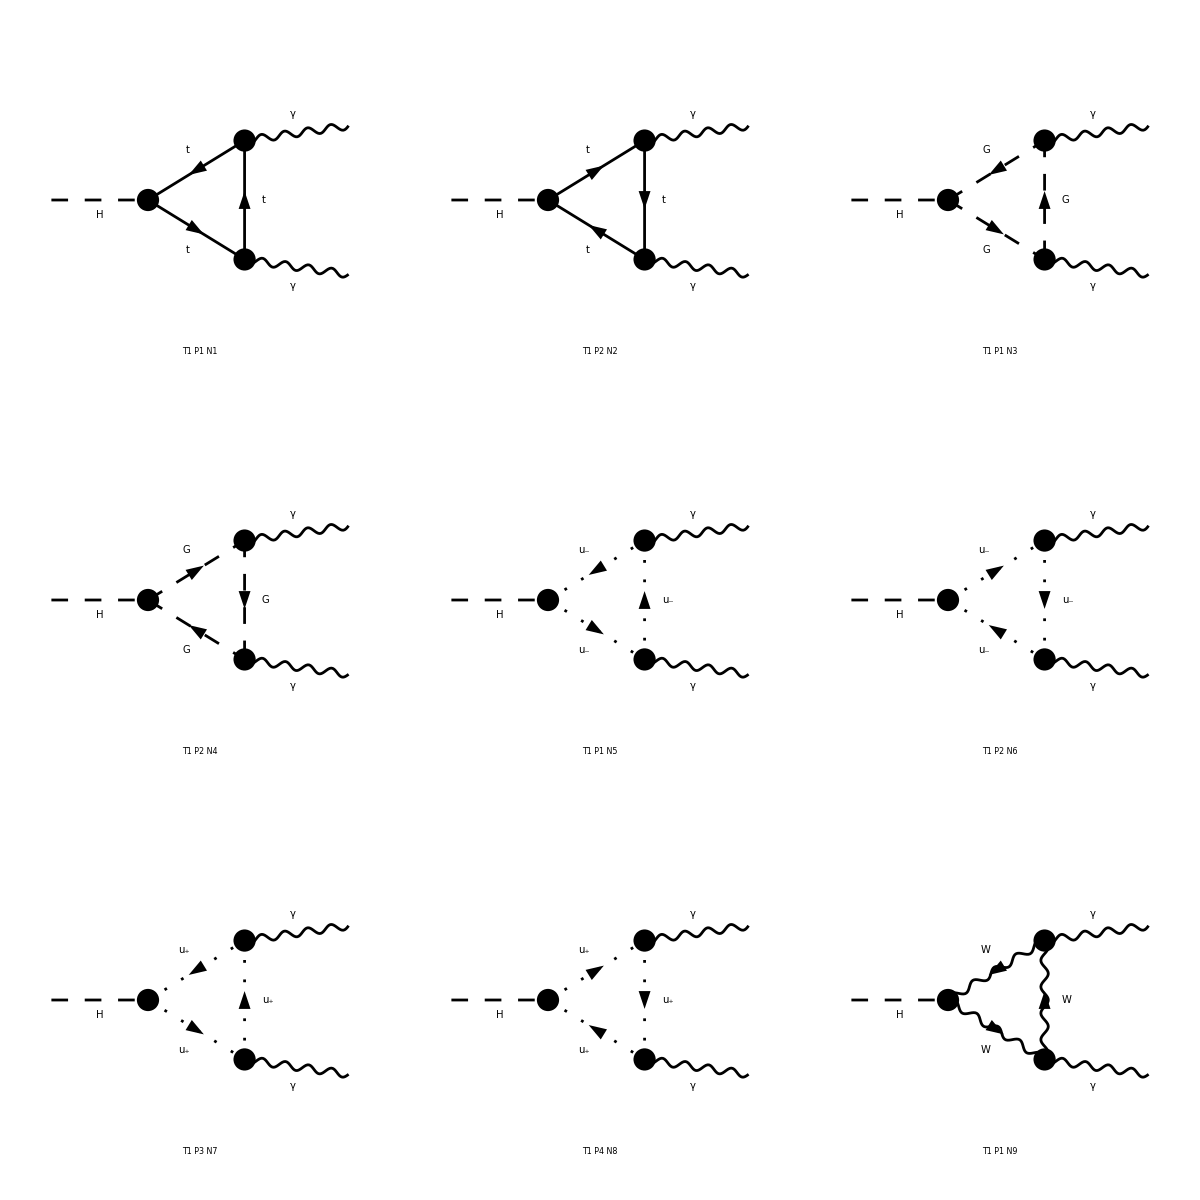

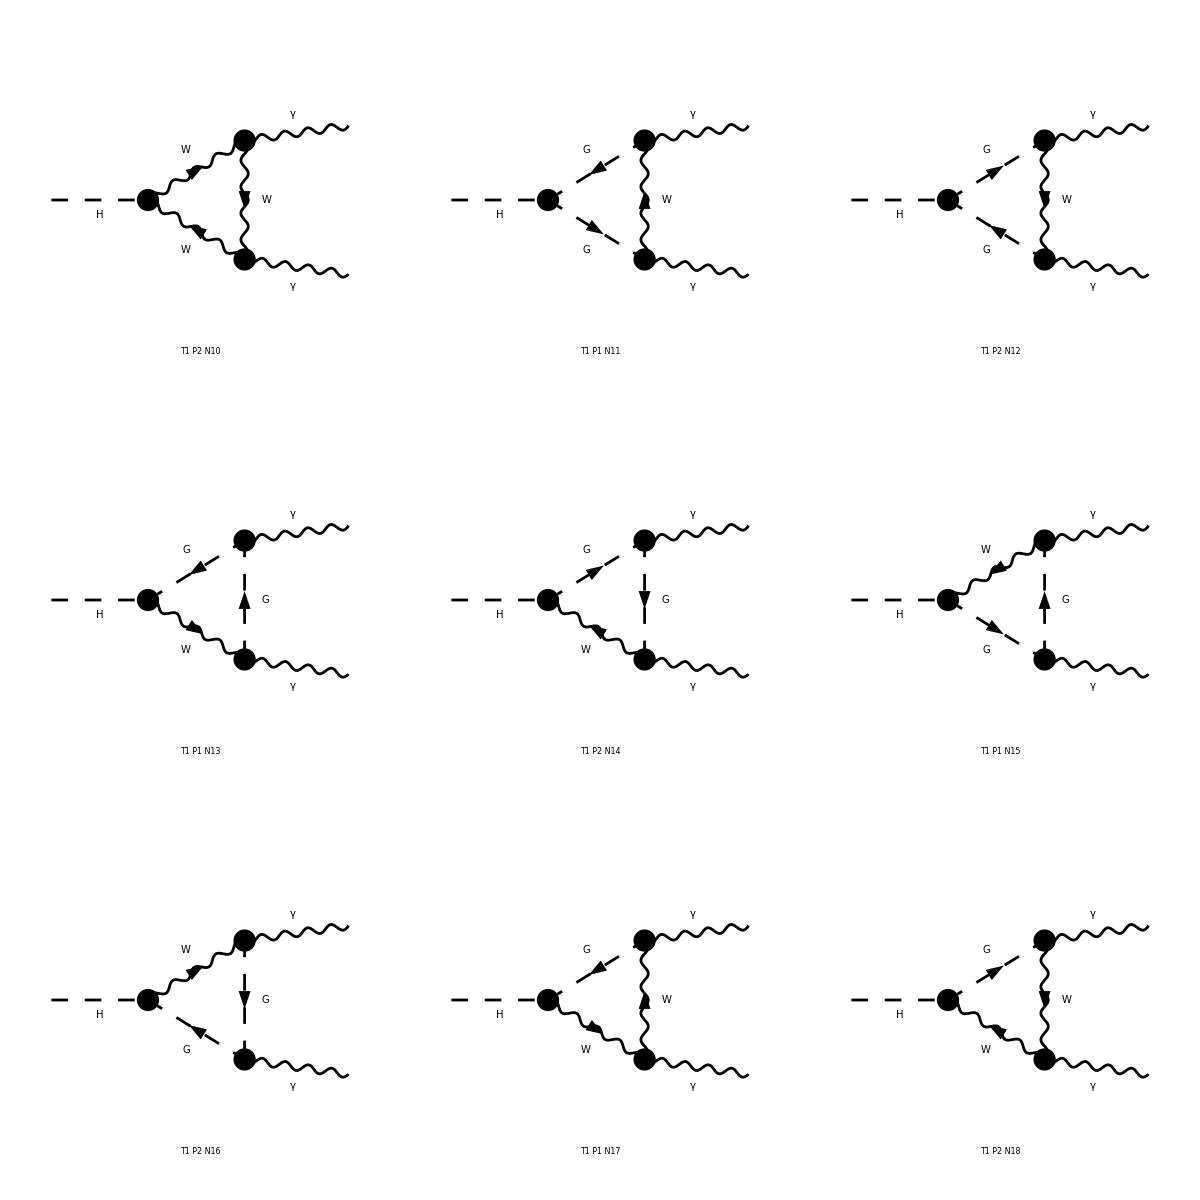

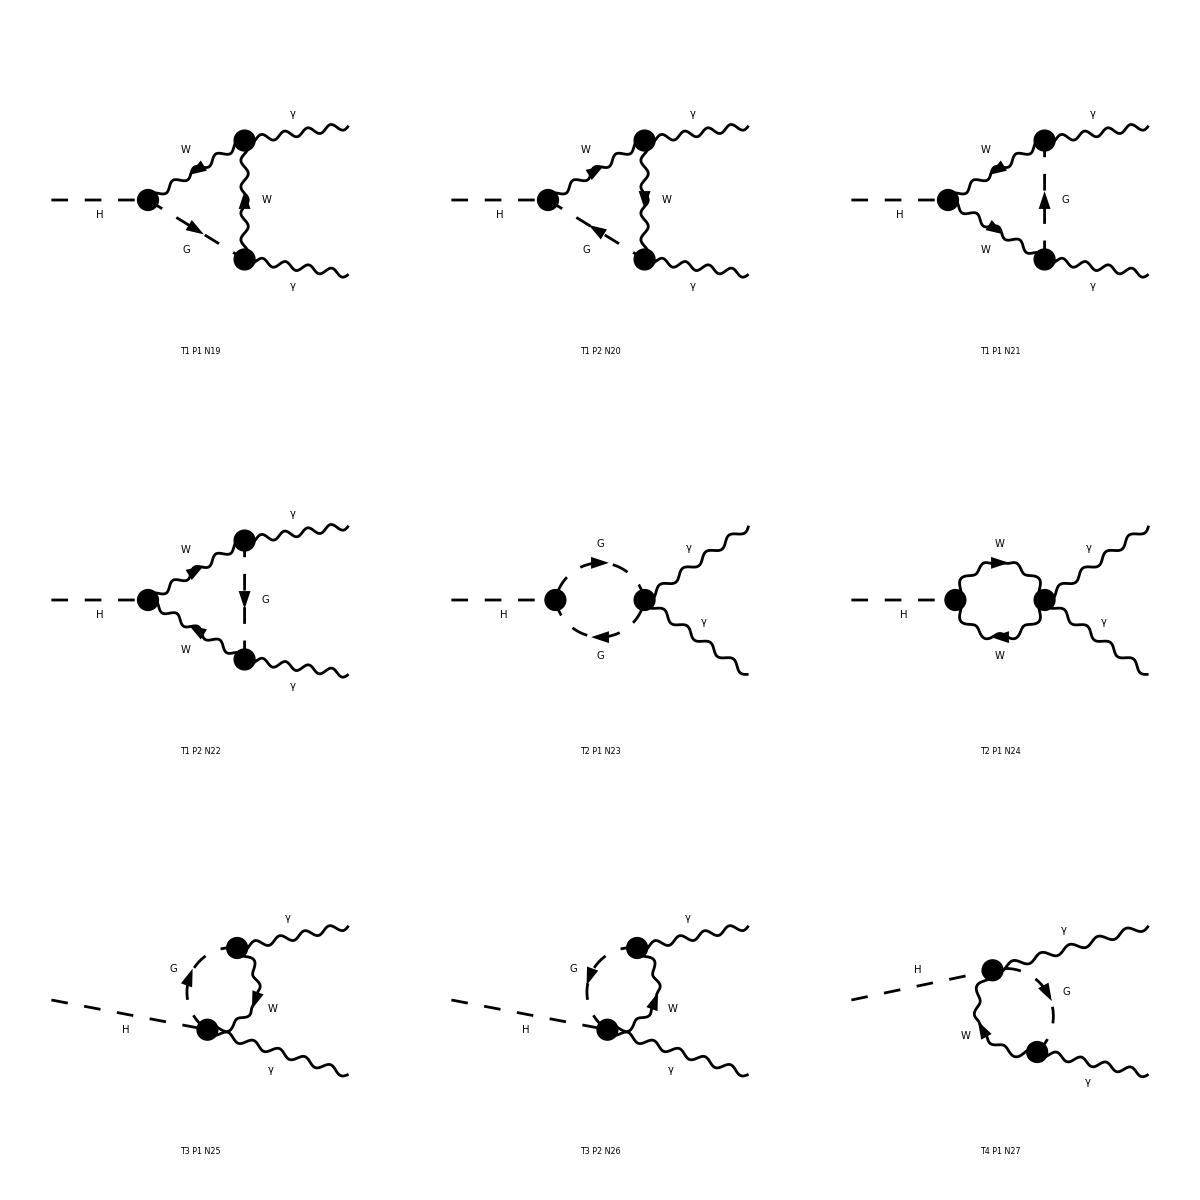

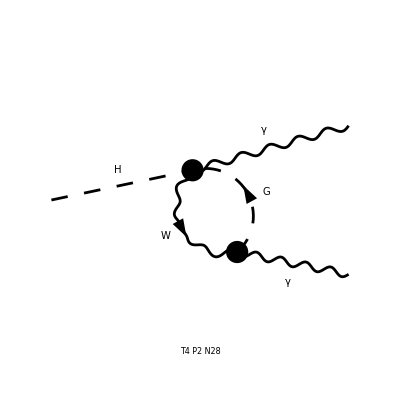

```mathematica
topo1=CreateTopologies[1,1->2,ExcludeTopologies->{Internal}];
diag1=InsertFields[topo1,{S[1]}->{V[1],V[1]},InsertionLevel->{Particles},Restrictions->NoLightFHCoupling];
Paint[diag1];
```

```mathematica
ClearProcess[];
amp=CalcFeynAmp[CreateFeynAmp[diag1],FermionChains->Chiral]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 22 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

in total: 28 Particles amplitudes

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

Amp[{MH}→{0,0}][(4 Alfa EL MT2 Pair1 B0i[bb0,0,MT2,MT2])/(3 MW π SW)-(3 Alfa EL (MH2/(6 MW)+MW) Pair1 B0i[bb0,MH2,MW2,MW2])/(2 π SW)+(-(4 Abb1 Alfa EL MT2)/(3 MW π SW)+(2 Alfa EL MH2 MT2 Pair1)/(3 MW π SW)) C0i[cc0,0,0,MH2,MT2,MT2,MT2]+(((8 Abb1+AbbSum1) Alfa EL MW)/(2 π SW)-(7 Alfa EL MH2 MW Pair1)/(4 π SW)) C0i[cc0,0,0,MH2,MW2,MW2,MW2]-(16 Alfa EL MT2 Pair1 C0i[cc00,0,0,MH2,MT2,MT2,MT2])/(3 MW π SW)+(6 Alfa EL (MH2/(6 MW)+MW) Pair1 C0i[cc00,0,0,MH2,MW2,MW2,MW2])/(π SW)+(Alfa EL MH2 MW Pair1 C0i[cc1,0,0,MH2,MW2,MW2,MW2])/(4 π SW)+(-(16 Abb3 Alfa EL MT2)/(3 MW π SW)+(4 Alfa EL MH2 MT2 Pair1)/(3 MW π SW)) C0i[cc2,0,0,MH2,MT2,MT2,MT2]+(-(3 (-(26 Abb1)/3+Abb3) Alfa EL MW)/(4 π SW)+(Abb2 Alfa EL ((4 MH2)/MW+MW))/(4 π SW)+(Alfa EL MH2 MW Pair1)/(2 π SW)) C0i[cc2,0,0,MH2,MW2,MW2,MW2]-(16 Abb2 Alfa EL MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]+C0i[cc22,0,0,MH2,MT2,MT2,MT2]))/(3 MW π SW)+(6 Abb2 Alfa EL (MH2/(6 MW)+MW) (C0i[cc12,0,0,MH2,MW2,MW2,MW2]+C0i[cc22,0,0,MH2,MW2,MW2,MW2]))/(π SW)]

To configm this diagram converges...

```mathematica
UVDivergentPart[amp]
```

Amp[{MH}→{0,0}][0]

PolarizationSum directory to the amplitude invokes SquaredME, HelicityME, and ColourME (with _Hel=0 option).

```mathematica
mat=PolarizationSum[amp,GaugeTerms->False]//Simplify
```

HelicityME::nomat: \!\(\*StyleBox["\"Warning: No matrix elements to compute.\"", "MT"]\)

ColourME::nomat: \!\(\*StyleBox["\"Warning: No matrix elements to compute.\"", "MT"]\)

preparing FORM code in /Users/misho/Documents/Dropbox/FeynLecture/fc1.frm

running FORM...

ok

1/(18 π SW2)Alfa Alfa2 (-1/MW2 16 MH2^2 MT2 C0i[cc0,0,0,MH2,MT2,MT2,MT2] (-4 MT2 (C0i[cc0,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-16 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+3 MH2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+18 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-16 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+3 MH2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+18 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-16 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+3 MH2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+18 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))-3 MH2 C0i[cc0,0,0,MH2,MW2,MW2,MW2] (-16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])+3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])+64 MH2 MT2 (C0i[cc0,0,0,MH2,MT2,MT2,MT2]Superscript[*])-195 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])+64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])-12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])-72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])-3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])+288 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])-54 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-324 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+272 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])-54 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-330 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+288 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])-54 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])-324 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))+1/MW2 16 MT2 B0i[bb0,0,MT2,MT2] (16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-16 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+42 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))-1/MW2 3 (MH2+6 MW2) B0i[bb0,MH2,MW2,MW2] (16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-16 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+42 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))-1/MW2 64 MT2 C0i[cc00,0,0,MH2,MT2,MT2,MT2] (16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-16 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+42 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))+1/MW2 12 (MH2+6 MW2) C0i[cc00,0,0,MH2,MW2,MW2,MW2] (16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-16 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+42 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))+3 MH2 C0i[cc1,0,0,MH2,MW2,MW2,MW2] (16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-16 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+42 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-32 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+6 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+36 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))-1/MW2 32 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]+C0i[cc22,0,0,MH2,MT2,MT2,MT2]) (16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])-8 MH2 MT2 (C0i[cc0,0,0,MH2,MT2,MT2,MT2]Superscript[*])+27 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-48 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+78 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))+1/MW2 6 MH2 (MH2+6 MW2) (C0i[cc12,0,0,MH2,MW2,MW2,MW2]+C0i[cc22,0,0,MH2,MW2,MW2,MW2]) (16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])-8 MH2 MT2 (C0i[cc0,0,0,MH2,MT2,MT2,MT2]Superscript[*])+27 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-48 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+78 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))-1/MW2 16 MH2 MT2 C0i[cc2,0,0,MH2,MT2,MT2,MT2] (16 MT2 (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2+6 MW2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])-16 MH2 MT2 (C0i[cc0,0,0,MH2,MT2,MT2,MT2]Superscript[*])+51 MH2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+72 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-96 MH2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+18 MH2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+108 MH2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-80 MH2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+18 MH2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+114 MH2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-96 MH2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+18 MH2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+108 MH2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*]))+1/MW2 6 MH2 C0i[cc2,0,0,MH2,MW2,MW2,MW2] (16 MT2 (MH2+7 MW2) (B0i[bb0,0,MT2,MT2]Superscript[*])-3 (MH2^2+13 MH2 MW2+42 MW2^2) (B0i[bb0,MH2,MW2,MW2]Superscript[*])-8 MH2^2 MT2 (C0i[cc0,0,0,MH2,MT2,MT2,MT2]Superscript[*])-48 MH2 MT2 MW2 (C0i[cc0,0,0,MH2,MT2,MT2,MT2]Superscript[*])+27 MH2^2 MW2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])+165 MH2 MW2^2 (C0i[cc0,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MH2 MT2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])-448 MT2 MW2 (C0i[cc00,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+156 MH2 MW2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+504 MW2^2 (C0i[cc00,0,0,MH2,MW2,MW2,MW2]Superscript[*])+3 MH2^2 MW2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])+21 MH2 MW2^2 (C0i[cc1,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MH2^2 MT2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])-416 MH2 MT2 MW2 (C0i[cc12,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^3 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+150 MH2^2 MW2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])+468 MH2 MW2^2 (C0i[cc12,0,0,MH2,MW2,MW2,MW2]Superscript[*])-48 MH2^2 MT2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])-304 MH2 MT2 MW2 (C0i[cc2,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^3 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+156 MH2^2 MW2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])+510 MH2 MW2^2 (C0i[cc2,0,0,MH2,MW2,MW2,MW2]Superscript[*])-64 MH2^2 MT2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])-416 MH2 MT2 MW2 (C0i[cc22,0,0,MH2,MT2,MT2,MT2]Superscript[*])+12 MH2^3 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+150 MH2^2 MW2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])+468 MH2 MW2^2 (C0i[cc22,0,0,MH2,MW2,MW2,MW2]Superscript[*])))

### Numerical Evaluation

```mathematica
Install["LoopTools"]
```

LinkObject[/usr/local/bin/LoopTools,9,9]

```mathematica
VALUES[higgs_]:={
Den[p2_,m2_]:>1/(p2-m2),
MT->173,MT2->173^2,
MW->80.4,MW2->80.4^2,
Alfa->1/128,Alfa2->1/128^2,
SW2->0.23,
MH->higgs,MH2->higgs^2}
MyResult[higgs_]:=mat//.VALUES[higgs]//Simplify
```

```mathematica
MyResult[125]
```

0.131154

### Compare to a literature

```mathematica
f[t_]:=If[t<1,-1/4(Log[(1+√(1-t))/(1-√(1-t))]-ⅈ π)^2,(ArcSin[√(1/t)])^2]
Fb[t_]:=2+3t+3t(2-t)f[t]
Ff[t_]:=-2t(1+(1-t)f[t])
Fs[t_]:=t(1-t f[t])
InSomePaper[higgs_]:=(Alfa MH2^2)/(8π SW2 MW2)Abs[Alfa*3*(2/3)^2 Ff[((2MT)/MH)^2]+Alfa*1*1^2 Fb[((2MW)/MH)^2]]^2//.VALUES[higgs]
```

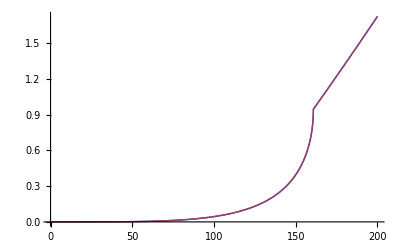

```mathematica
Plot[{MyResult[mh],InSomePaper[mh]},{mh,0,200}]
```

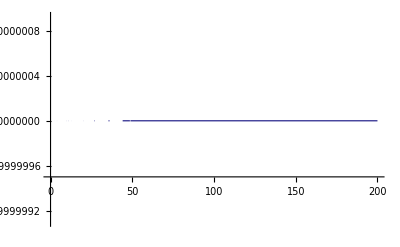

```mathematica
Plot[{MyResult[mh]/InSomePaper[mh]},{mh,0,200}]
```